Basic Functions for computing feedforward and testing on dynamics

```mathematica
Clear["Global`*"];
ffCartPendulumGeneral[n_,τ_,τ1_,A_]:=Module[{x,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={xdot,1/(1-A Cos[θ]^2)(A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2)(λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),θdot,1/(1-A Cos[θ]^2)(-1/(1-A Cos[θ]^2)(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),0,-λ1,2/(A Cos[2 θ]+A-2)^3 (Cos[θ] (4 Sin[θ] (A λ4^2 Cos[2 θ]+4 A λ2^2+(A+2) λ4^2)-(A Cos[2 θ]-3 A+2) (A Cos[2 θ]+A-2) (A θdot^2 λ2-λ4))+A ((A-2) Cos[2 θ]+A) (A Cos[2 θ]+A-2) (λ2-θdot^2 λ4)-4 λ2 λ4 Sin[θ] (3 A Cos[2 θ]+3 A+2)),4/(A Cos[2 θ]+A-2)(A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3};
bcs={Subscript[x, 0]==Subscript[xdot, 0]==Subscript[x, n]==Subscript[xdot, n]==Subscript[θ, 0]==Subscript[θdot, 0]==Subscript[θdot, n]==0,Subscript[θ, n]==π};eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];sv=Flatten[Table[{{Subscript[x, i],0},{Subscript[xdot, i],0},{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0},{Subscript[λ3, i],0},{Subscript[λ4, i],0}},{i,0,n}],1];froot=Quiet[FindRoot[eqns,sv]];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2)(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/.froot,{0,τ},InterpolationOrder->1];

xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];

{xff,xdotff,θff,θdotff,uff}]
```

```mathematica
TestSwingUpGeneral[τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2)(uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2)(-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==xdot[0]==θ[0]==θdot[0]==0};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
{xs,θs}]
```

Numerical Studies with varying values of N

```mathematica
SimExpt1[n_,τ_] :=Module[{A,τ1,xff1,xffdot1,θff1,θffdot1,x1,θ1,uff1,},
A=0.4; 
τ1= τ*1.25 ;
{xff1,xffdot1,θff1,θffdot1,uff1}=ffCartPendulumGeneral[n,τ,τ1,A];
{x1,θ1}=TestSwingUpGeneral[τ,τ1,uff1,A]; 
p1a=Plot[{θff1[t],uff1[t],xff1[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{θ,uff,x},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1b=Plot[{θ1[t],uff1[t],x1[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{θ,uff,x},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
Grid[{{p1a,p1b}}]]
```

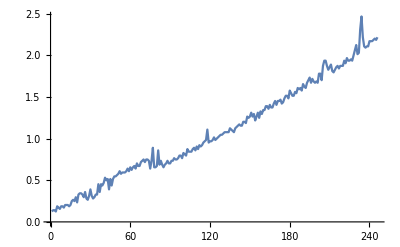

```mathematica
N1 = 5;N2 = 250;τ = 20;
TimingData =Flatten[Table[Timing[SimExpt1[i,τ];],{i,N1,N2}]];
ListLinePlot[Table[TimingData[[i]],{i,1,2*(N2-N1+1),2}]]
```

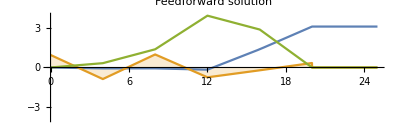
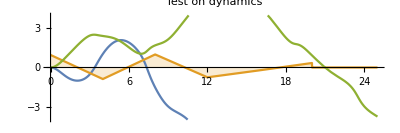
-Graphics- | -Graphics-

```mathematica
SimExpt1[5,τ]
```